```mathematica
InCyl[h_,t_,x_,y_,z_,L_,R_]:=(
hv={0,0,h};
xv={x,y,z};
dv=xv-hv;
rv={Cos[t],0,Sin[t]};
hv2=hv+L*rv;
dv2=xv-hv2;
proj2=dv2.rv;
proj=dv.rv;
norm=Norm[dv]*Sin[ArcCos[dv.rv/Norm[dv]]];
If[(proj>=0&&proj<=L&&norm<=R)||
(proj≤0&&Norm[dv]≤R)||
(proj2≥0&&Norm[dv2]≤R),1,0]
)
BelowCyl[h_,t_,x_,y_,z_,L_,R_]:=(
hv={0,0,h};
xv={x,y,z};
dv=xv-hv;
rv={Cos[t],0,Sin[t]};
hv2=hv+L*rv;
dv2=xv-hv2;
proj2=dv2.rv;
proj=dv.rv;
norm=Norm[dv]*Sin[ArcCos[dv.rv/Norm[dv]]];
If[(
(proj>=0&&proj<=L&&norm<=R)||
(proj≤0&&Norm[dv]≤R)||
(proj2≥0&&Norm[dv2]≤R)
)
&&z<0,1,0]
)
Ener[F_,h_,t_,a_,b_]:=(
SA=NIntegrate[InCyl[h,t,x,y,0,L,R],{x,-L-R,L+R},{y,-L-R,L+R}];
VOL=NIntegrate[BelowCyl[h,t,x,y,z,L,R],{x,-L-R,L+R},{y,-L-R,L+R},{z,-L-R,L+R}];
If[VOL>4*π/3,Print["ERROR"]];
d=1+((1-ⅈ √3) π^(1/3))/(2^(2/3) (-2 π+3 VOL+√3 √(-4 π VOL+3 VOL^2))^(1/3))+((1+ⅈ √3) (-2 π+3 VOL+√3 √(-4 π VOL+3 VOL^2))^(1/3))/(2 (2 π)^(1/3));
0.5*a*d^(5/2)
)
```

```mathematica
LL={};
xL={};
For[L=0,L<1,
Y=10000;
A0=10000;
R=1;
dE={};
di={};
For[hi=0.0,hi<0.1,
hi=hi+0.01;
Ei=Re[Ener[100000,1-hi,0,Y,A0]];
AppendTo[dE,Ei];
AppendTo[di,hi];
];
EL=Transpose[{di,dE}];
ES=Interpolation[EL,Method->"Spline"];
MT=Fit[Log10[EL],{1,x},x];
xeff=MT[[2]]/.x->1;
AppendTo[LL,L];
AppendTo[xL,xeff];
L=L+0.1;
]
```

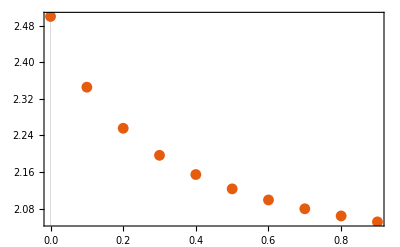

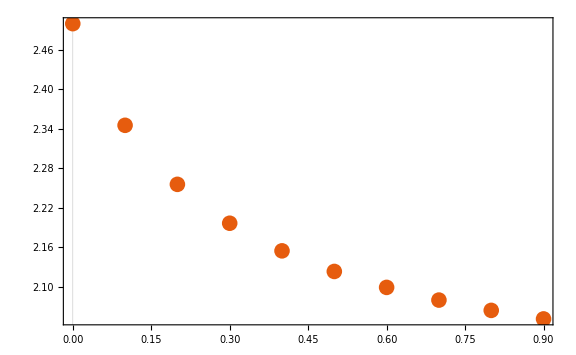

/Users/farzanberoz/Desktop/biophysics/biofilms/1d-film/analysis/plots/x-vs-l.png

```mathematica
lx=Transpose[{LL,xL}];
FIGN=ListPlot[lx,PlotTheme->"Scientific"]
plot=Show[{FIGN},ImageSize->Large,LabelStyle->Directive[Large]]
Export["/Users/farzanberoz/Desktop/biophysics/biofilms/1d-film/analysis/plots/x-vs-l.png",plot]
```

```mathematica
Y=10000;
A0=10000;
L=0.5;
R=1;
dE={};
di={};
For[hi=0.0,hi<0.1,
hi=hi+0.01;
Ei=Re[Ener[100000,1-hi,0,Y,A0]];
AppendTo[dE,Ei];
AppendTo[di,hi];
];
EL=Transpose[{di,dE}];
```

```mathematica
LL
```

{0,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9}

{{-2.,-0.545736},{-1.69897,0.0737824},{-1.52288,0.44305},{-1.39794,0.708423},{-1.30103,0.916292},{-1.22185,1.0875},{-1.1549,1.23323},{-1.09691,1.36021},{-1.04576,1.47279},{-1.,1.57397}}

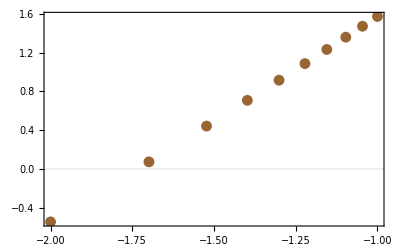

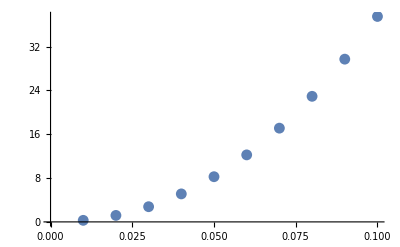

3.68621+2.12337 x

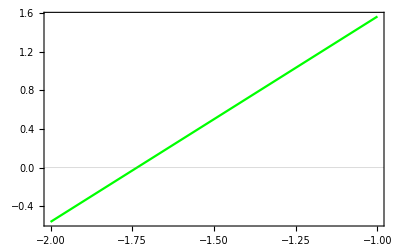

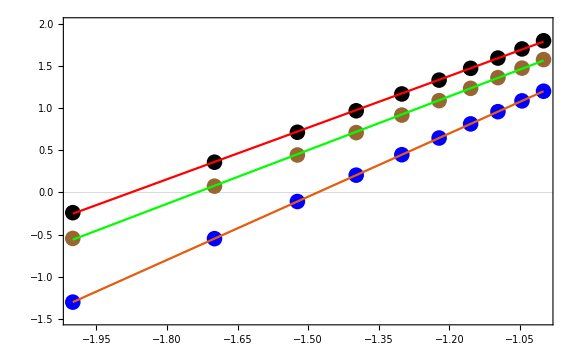

/Users/farzanberoz/Desktop/biophysics/biofilms/1d-film/analysis/plots/d-vs-e.png

```mathematica
Log10[EL]
FIGI2=ListPlot[Log10[EL],PlotTheme->"Scientific",PlotStyle->Brown]
ListPlot[EL]
MT=Fit[Log10[EL],{1,x},x]
FIG02=Plot[MT,{x,-2,-1},PlotTheme->"Scientific",PlotStyle->Green]
plot=Show[{FIGI,FIG0,FIGI2,FIG02,FIGI3,FIG03},ImageSize->Large,LabelStyle->Directive[Large],PlotRange->{-1.5,2.0}]
Export["/Users/farzanberoz/Desktop/biophysics/biofilms/1d-film/analysis/plots/d-vs-e.png",plot]
```

```mathematica
MT[[2]]/.x->1
```

2.22345

```mathematica
EL
```

{{0,-1.37909×10^-36},{0.01,1.25107},{0.02,4.81447},{0.03,10.6849},{0.04,18.906},{0.05,29.5319},{0.06,42.6206},{0.07,58.2322},{0.08,76.4277},{0.09,97.269},{0.1,120.819},{0.2,519.63},{0.3,1265.97},{0.4,2449.12},{0.5,4199.23},{0.6,6736.51},{0.7,51029.9},{0.8,41204.9}}

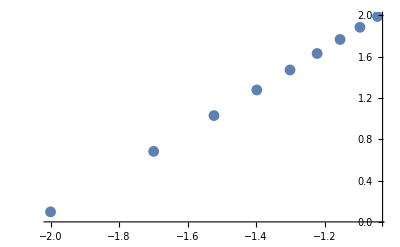

```mathematica
FIG0
```

4.06019+1.98644 x

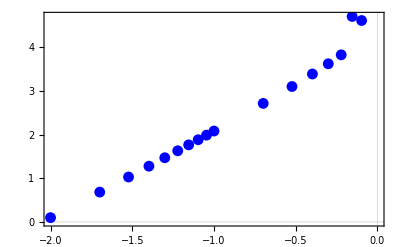

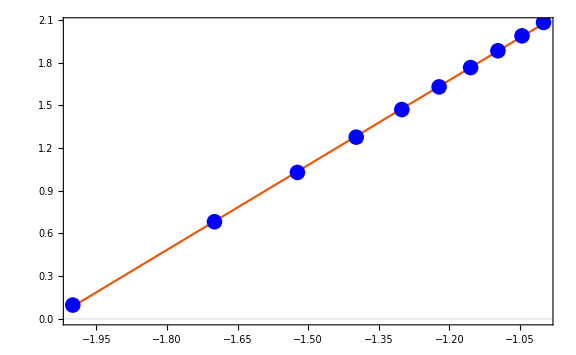

```mathematica
ELT={{0.01,1.2510740137791145},{0.02,4.8144723550369175},{0.03,10.684907028716804},{0.04,18.906016236908318},{0.05,29.53190228320654},{0.060000000000000005,42.62064080314915},{0.07,58.23220258340069},{0.08,76.42767738582968},{0.09,97.26895934496885},{0.1,120.81863529462073}};
ELOG=Log10[ELT];
EF=Fit[ELOG,{1,x},x]
FIG0=ListPlot[Log10[EL],PlotTheme->"Scientific",PlotStyle->Blue]
FIGI=Plot[EF,{x,-2,-1},PlotTheme->"Scientific"];
Show[{FIGI,FIG0},ImageSize->Large,LabelStyle->Directive[Large]]
```

Fit::fitm: Unable to solve for the fit parameters; the design matrix is nonrectangular, non-numerical, or could not be inverted.

Show::gcomb: Could not combine the graphics objects in {Fit[{{-∞, -35.86040724066441` + 1.3643763538418412` ⅈ}, {-2.`, 0.09728300339847153`}, {-1.6989700043360187`, 0.682548697306346`}, {-1.5228787452803376`, 1.0287707476427246`}, {-1.3979400086720375`, 1.2766000265395885`}, « 9 », {-0.3010299956639812`, 3.623169718767703`}, {-0.2218487496163564`, 3.8284347938890133`}, {-0.1549019599857432`, 4.7078250500053604`}, {-0.09691001300805645`, 4.614948383350405`}}, {1, x}, x], GraphicsBox[List[List[], List[List[List[], List[Hue[Skeleton[3]], Directive[Skeleton[3]], PointBox[Skeleton[1]]], List[]]], List[]], List[Rule[DisplayFunction, Identity], Rule[PlotRangePadding, List[List[Scaled[Skeleton[1]], Scaled[Skeleton[1]]], List[Scaled[Skeleton[1]], Scaled[Skeleton[1]]]]], Rule[AxesOrigin, List[0, 0]], Rule[PlotRange, List[List[-2.`, 0], List[0, 4.7078250500053604`]]], Rule[DisplayFunction, Identity], Rule[AspectRatio, NCache[Power[GoldenRatio, -1], 0.6180339887498948`]], Rule[Axes, List[True, True]], Rule[AxesLabel, List[None, None]], Rule[AxesOrigin, List[0, 0]], RuleDelayed[DisplayFunction, Identity], Rule[Frame, List[List[False, False], List[False, False]]], Rule[FrameLabel, List[List[None, None], List[None, None]]], Rule[FrameTicks, List[List[Automatic, Automatic], List[Automatic, Automatic]]], Rule[GridLines, List[None, None]], Rule[GridLinesStyle, Directive[GrayLevel[0.5`, 0.4`]]], Rule[Method, List[]], Rule[PlotRange, List[List[-2.`, 0], List[0, 4.7078250500053604`]]], Rule[PlotRangeClipping, True], Rule[PlotRangePadding, List[List[Scaled[Skeleton[1]], Scaled[Skeleton[1]]], List[Scaled[Skeleton[1]], Scaled[Skeleton[1]]]]], Rule[Ticks, List[Automatic, Automatic]]]]}.

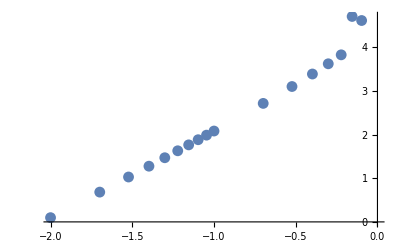
Show[{Fit[{{-∞,-35.8604+1.36438 ⅈ},{-2.,0.097283},{-1.69897,0.682549},{-1.52288,1.02877},{-1.39794,1.2766},{-1.30103,1.47029},{-1.22185,1.62962},{-1.1549,1.76516},{-1.09691,1.88325},{-1.04576,1.98797},{-1.,2.08213},{-0.69897,2.71569},{-0.522879,3.10242},{-0.39794,3.38901},{-0.30103,3.62317},{-0.221849,3.82843},{-0.154902,4.70783},{-0.09691,4.61495}},{1,x},x],-Graphics-}]

```mathematica
Show[{FIGI,FIG0}]
```

4.05358+1.98234 x

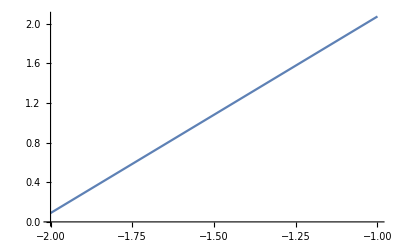

```mathematica
ELOG={{-2.,0.09728300339847153},{-1.6989700043360187,0.682548697306346},{-1.5228787452803376,1.0287707476427246},{-1.3979400086720375,1.2766000265395885},{-1.3010299956639813,1.4702914227351762},{-1.2218487496163564,1.629619975063297},{-1.154901959985743,1.765163217237098},{-1.0969100130080565,1.8832506617065934},{-1.0457574905606752,1.9879742694978195}};
EF=Fit[ELOG,{1,x},x]
FIGI=Plot[EF,{x,-2,-1}]
```

```mathematica
FS=ES';
Plot[Evaluate[ES[x]],{x,0,π/2}]
Plot[Evaluate[{ES[x],FS[x]}],{x,0,π/2}]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate :: izero will be suppressed during this calculation.

{{0,499942.},{0.1,497462.},{0.2,490019.},{0.3,477660.},{0.4,460524.},{0.5,438786.},{0.6,412663.},{0.7,382417.},{0.8,348350.},{0.9,310801.},{1.,270148.},{1.1,226795.},{1.2,181175.},{1.3,133746.},{1.4,84980.1},{1.5,35365.1}}

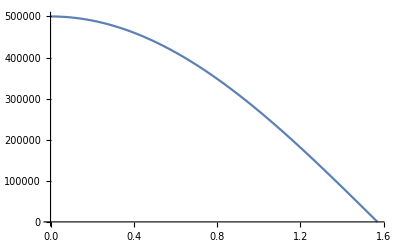

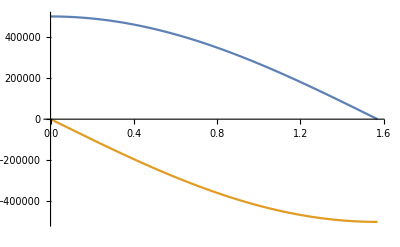

```mathematica
L=5;
R=1;
h0=0.4;
di={};
dE={};
For[i=0,i<π/2,
Ei=Re[Ener[100000,h0,i,1,1]];
AppendTo[dE,Ei];
AppendTo[di,i];
i=i+0.1;
]
EL=Transpose[{di,dE}]
ES=Interpolation[EL,Method->"Spline"];
FS=ES';
Plot[Evaluate[ES[x]],{x,0,π/2}]
Plot[Evaluate[{ES[x],FS[x]}],{x,0,π/2}]
```

```mathematica
s=NDSolve[{θ''[t]+FS[θ[t]]==0,θ[0]==0.1,θ'[0]==0},θ,{t,0,1}];
dt={};
dθ={};
For[q=0,q<0.005,
Print[q];
dd=Evaluate[{θ[q]}/.s][[1]];
dd=dd[[1]];
(*gt=Graphics3D[Cylinder[{{0,0,h0},{L*Cos[dd],0,L*Sin[dd]+h0}},R]];*)
I0=RegionPlot3D[InCyl[0.4,dd,x,y,z,L,R]==1,{x,-7,7},{y,-7,7},{z,-7,7},Mesh->None,PlotPoints->20,PlotStyle->Directive[Green,Opacity[0.8]],Boxed->False,BoundaryStyle->None,ImageSize->600,Axes->False,{AutomaticImageSize->True,ImageSize->{339.18259133765986,255.6270308766238},ViewAngle->0.35526726874693176,ViewCenter->{{0.5,0.5,0.5},{0.531397399076027,0.5156986995380135}},ViewPoint->{1.362724659126063,-2.6229425429410966,1.6471654196951353},ViewVertical->{0.005417428881886327,-0.16642658161209425,0.9860389669770778}}];
(*I0=Show[gt,{AutomaticImageSize->True,ImageSize->{339.18259133765986,255.6270308766238},ViewAngle->0.35526726874693176,ViewCenter->{{0.5,0.5,0.5},{0.531397399076027,0.5156986995380135}},ViewPoint->{1.362724659126063,-2.6229425429410966,1.6471654196951353},ViewVertical->{0.005417428881886327,-0.16642658161209425,0.9860389669770778}}];*)

AppendTo[dt,I0];
q=q+0.0001;
]
```

```mathematica
dt
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
Image0=Show[dt[[1]],{AutomaticImageSize->True,ImageSize->{339.18259133765986,255.6270308766238},ViewAngle->0.35526726874693176,ViewCenter->{{0.5,0.5,0.5},{0.531397399076027,0.5156986995380135}},ViewPoint->{1.362724659126063,-2.6229425429410966,1.6471654196951353},ViewVertical->{0.005417428881886327,-0.16642658161209425,0.9860389669770778}}];
```

```mathematica
ListAnimate[dt]
```

```mathematica
-Graphics3D-//Options
```

{AutomaticImageSize→True,ImageSize→{339.183,255.627},ViewAngle→0.355267,ViewCenter→{{0.5,0.5,0.5},{0.531397,0.515699}},ViewPoint→{1.36272,-2.62294,1.64717},ViewVertical→{0.00541743,-0.166427,0.986039}}

```mathematica
Export["/Users/farzanberoz/Desktop/popcylfixed.gif",dt]
```

/Users/farzanberoz/Desktop/popcylfixed.gif

```mathematica
normal={-1,0,0};
st=SphericalPlot3D[1,{θ,0,π},{ϕ,0,2 π},RegionFunction->Function[{x,y,z,θ,ϕ,r},{x,y,z}.normal≥0],PlotStyle->Directive[Green,Opacity[0.7],Specularity[White,10]],Mesh->None];
gt=Graphics3D[{Green,Opacity[0.7],Cylinder[{{0,0,0},{L,0,0}},R]}];
Show[{gt, st}]
```

-Graphics3D-

```mathematica
Show[{gt, st}]
```

-Graphics3D-

```mathematica
gt=Graphics3D[Cylinder[{{0,0,h0},{L*Cos[dd],0,L*Sin[dd]+h0}},R]];
```

```mathematica
RegionPlot3D[InCyl[0.4,0,x,y,z,L,R]==1,{x,-7,7},{y,-7,7},{z,-7,7},Mesh->None,PlotPoints->20,PlotStyle->Directive[Green,Opacity[0.8]],Boxed->False,BoundaryStyle->None,ImageSize->600,Axes->False]
```

```mathematica
-Graphics3D-//Options
```

{BoxRatios→{1,1,1},Boxed→False,DisplayFunction→Identity,FaceGridsStyle→Automatic,ImageSize→600,Method→{DefaultBoundaryStyle→Directive[-Graphics-]},PlotRange→{{-7,7},{-7,7},{-7,7}},PlotRangePadding→{Scaled[0.02],Scaled[0.02],Scaled[0.02]},Ticks→{Automatic,Automatic,Automatic},ViewPoint→{0.161263,-2.62143,2.13357},ViewVertical→{0.0439456,0.051777,0.997691}}

```mathematica
Solve[π/3 d^2(3*1-d)==V,d]
```

{{d→1-(2 π)^(1/3)/((-2 π+3 V+√3 √(-4 π V+3 V^2))^(1/3))-((-2 π+3 V+√3 √(-4 π V+3 V^2))^(1/3))/(2 π)^(1/3)},{d→1+((1+ⅈ √3) π^(1/3))/(2^(2/3) (-2 π+3 V+√3 √(-4 π V+3 V^2))^(1/3))+((1-ⅈ √3) (-2 π+3 V+√3 √(-4 π V+3 V^2))^(1/3))/(2 (2 π)^(1/3))},{d→1+((1-ⅈ √3) π^(1/3))/(2^(2/3) (-2 π+3 V+√3 √(-4 π V+3 V^2))^(1/3))+((1+ⅈ √3) (-2 π+3 V+√3 √(-4 π V+3 V^2))^(1/3))/(2 (2 π)^(1/3))}}

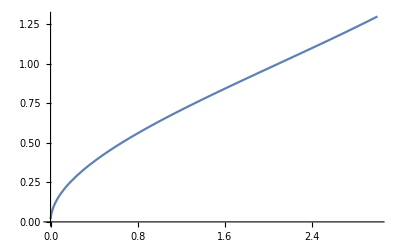

```mathematica
Plot[1+((1-ⅈ √3) π^(1/3))/(2^(2/3) (-2 π+3 V+√3 √(-4 π V+3 V^2))^(1/3))+((1+ⅈ √3) (-2 π+3 V+√3 √(-4 π V+3 V^2))^(1/3))/(2 (2 π)^(1/3)),{V,0,3}]
```